```mathematica
SetDirectory[NotebookDirectory[]];

gfactor=Import["g-factor","TSV"];
energy=Import["energies","TSV"];
```

```mathematica
gfactor[[1]][[2]]
```

1.73001

```mathematica
gfactor//Dimensions
```

{50,5}

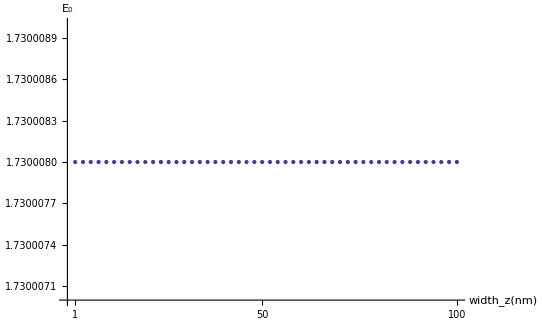

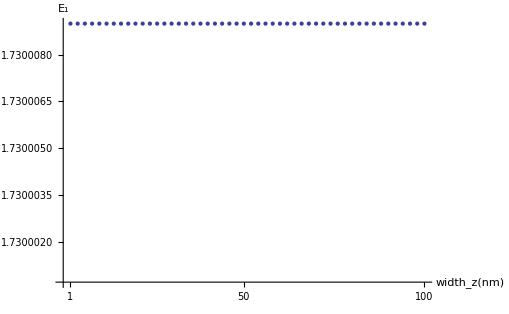

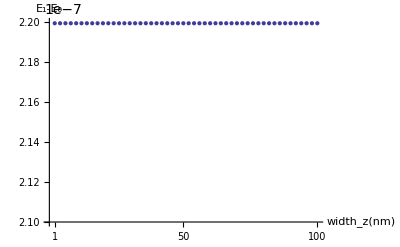

```mathematica
ListPlot[Table[gfactor[[i]][[2]],{i,1,50}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_0"},PlotRange->{1.730007,1.730009}]

ListPlot[Table[gfactor[[i]][[3]],{i,1,50}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_1"},PlotRange->{1.7300007,1.730009}]

ListPlot[Table[gfactor[[i]][[4]],{i,1,50}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_1-E_0"},PlotRange->{2.1*10^-7,2.2*10^-7}]
```

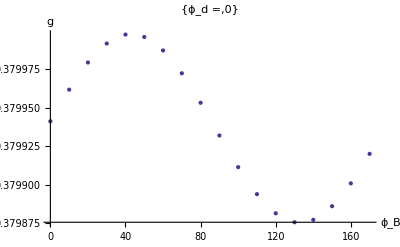
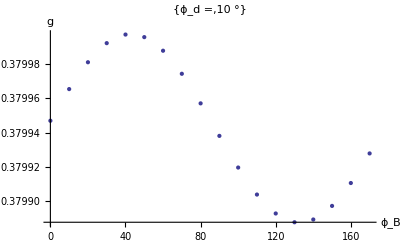
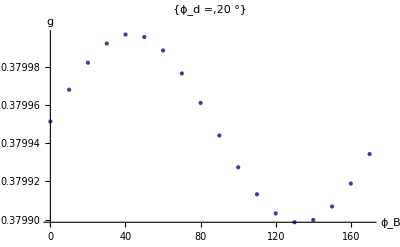
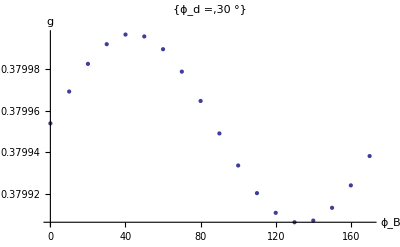
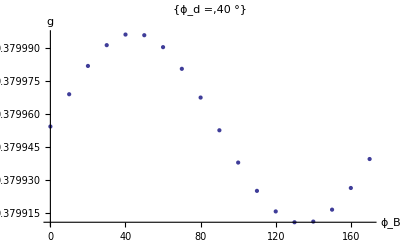
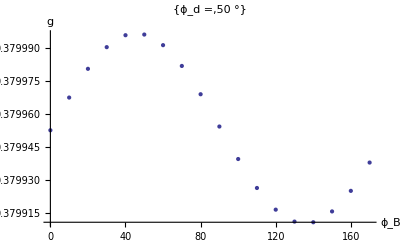
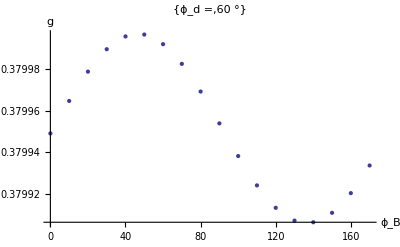
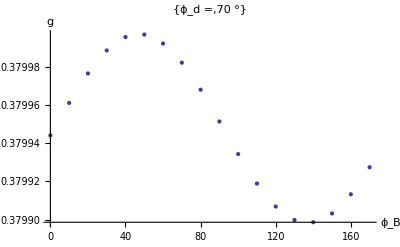

```mathematica
Table[ListPlot[Table[{gfactor[[i]][[1]],gfactor[[i]][[5]]},{i,1+18*j,18+18*j}],AxesLabel->{"ϕ_B","g"},PlotLabel->{"ϕ_d =",j*10 "°"}],{j,0,17}]
```

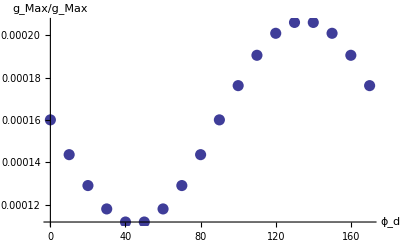

```mathematica
ListPlot[Table[{j*10,(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]-Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])/(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]+Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])},{j,0,17}],AxesLabel->{"ϕ_d","g_Max/g_Max"},PlotStyle->Directive[PointSize->0.02]]
```